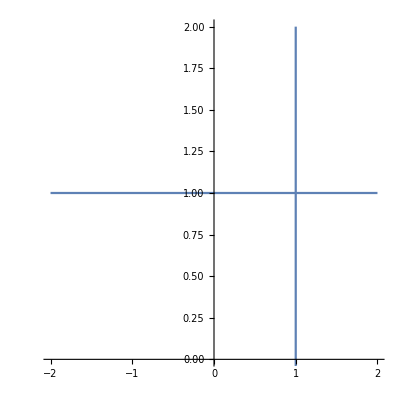

```mathematica
Show[ParametricPlot[{x,#},{x,-2,2},AspectRatio->1],ParametricPlot[{#,y},{y,-2,2}]]&[1,2]
```

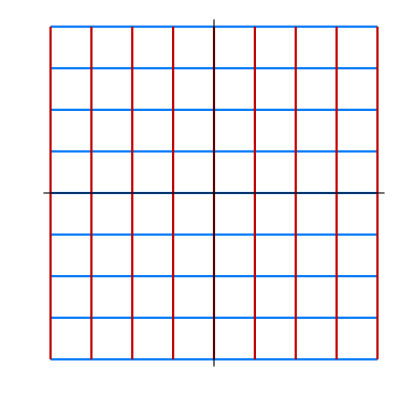

```mathematica
Show[Table[ParametricPlot[{x,i},{x,-4,4},PlotStyle->RGBColor[0.,0.47,0.98]
],{i,-4,4}],Table[ParametricPlot[{i,y},{y,-4,4},PlotStyle->RGBColor[0.75,0.,0.]],{i,-4,4}],PlotRange->{-4,4},AspectRatio->1,Ticks->None]
```

```mathematica
Show[%6,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.415]],Method->{"ScalingFunctions"->None}]
```

-Graphics-

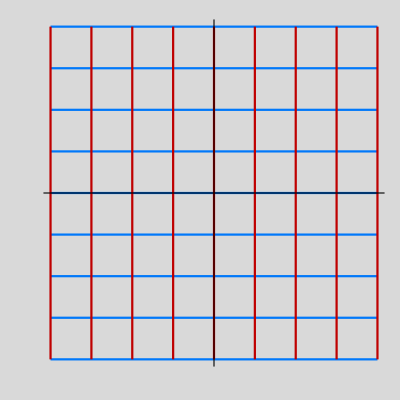

```mathematica
Show[%7,Background->LightGray]
```

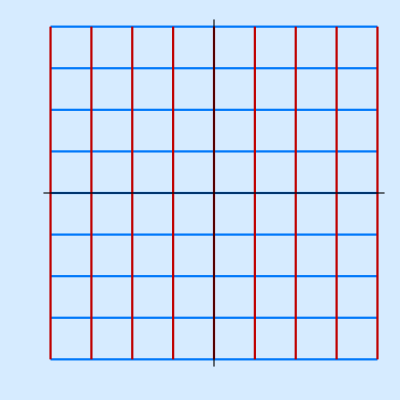

```mathematica
Show[%7,Background->RGBColor[0.84,0.92,1.]]
```

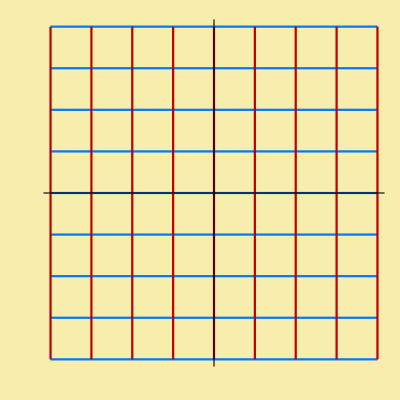

```mathematica
Show[%7,Background->RGBColor[0.97,0.93,0.68]]
```

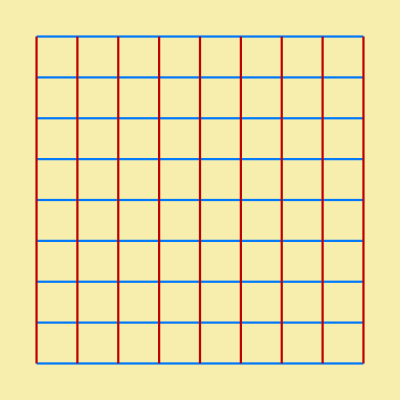

```mathematica
Show[%8,Axes->False]
```

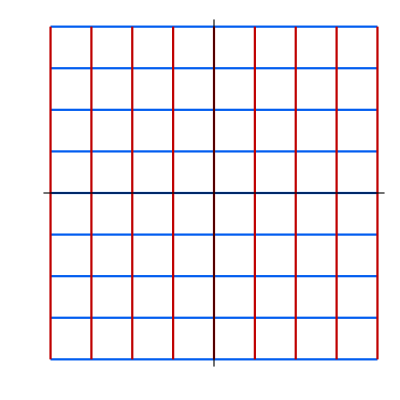

```mathematica
Show[%3,AxesStyle->Black]
```

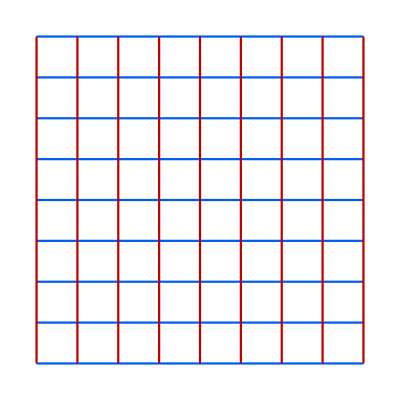

```mathematica
Show[%4,Axes->False]
```

```mathematica
Show[%4,AxesStyle->Black]
```

-Graphics-

```mathematica
z=x+I y
```

x+ⅈ y

```mathematica
Clear@y
```

```mathematica
z^2
```

(x+ⅈ y)^2

```mathematica
Expand[(x+ⅈ y)^2]
```

x^2+2 ⅈ x y-y^2

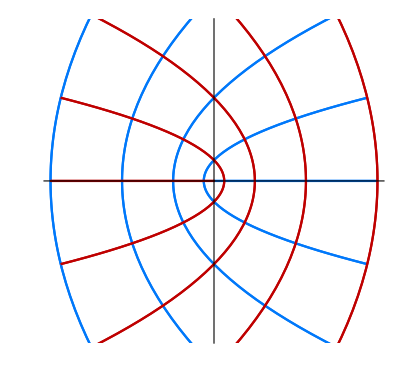

```mathematica
Show[Table[ParametricPlot[{x^2-i^2,2x i},{x,-4,4},PlotStyle->RGBColor[0.,0.47,0.98]],{i,-4,4}],Table[ParametricPlot[{i^2-y^2,2 i y },{y,-4,4},PlotStyle->RGBColor[0.75,0.,0.]],{i,-4,4}],PlotRange->{-15,15},Ticks->None]
```

```mathematica
Show[%11,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.34]],Method->{"ScalingFunctions"->None}]
```

-Graphics-

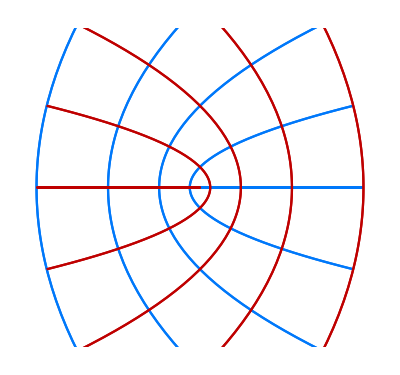

```mathematica
Show[%12,Axes->False]
```

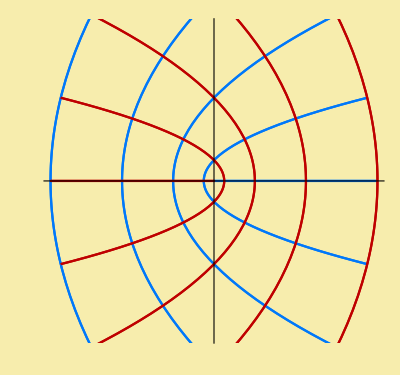

```mathematica
Show[%12,Background->RGBColor[0.97,0.93,0.68]]
```

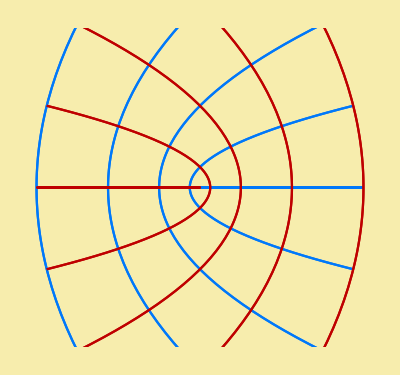

```mathematica
Show[%13,Axes->False]
```

```mathematica
1/z
```

```mathematica
Re[1/(x+ⅈ y)]
```

Re[1/(x+ⅈ y)]

```mathematica
Simplify[Re[1/(x+ⅈ y)]]
```

Re[1/(x+ⅈ y)]

```mathematica
ComplexExpand[Im[1/(x+ⅈ y)]]
```

-y/(x^2+y^2)

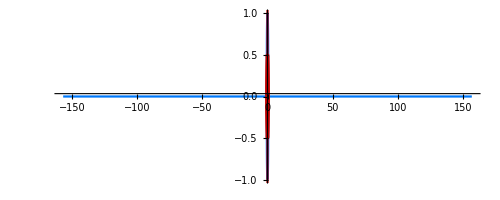

```mathematica
Show[Table[ParametricPlot[{x/(x^2+i^2),-i/(x^2+i^2)},{x,-10,10},PlotStyle->RGBColor[0.,0.47,0.98]],{i,-4,4}],Table[ParametricPlot[{i/(i^2+y^2),-y/(i^2+y^2) },{y,-10,10},PlotStyle->RGBColor[0.75,0.,0.]],{i,-4,4}],PlotRange->{-1,1}]
```

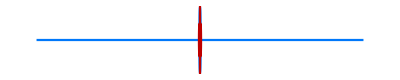

```mathematica
Show[%20,Axes->False]
```

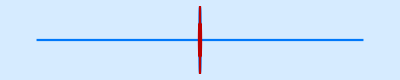

```mathematica
Show[%21,Background->RGBColor[0.84,0.92,1.]]
```

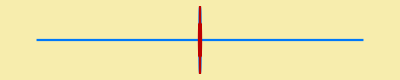

```mathematica
Show[%24,Background->RGBColor[0.97,0.93,0.68]]
```

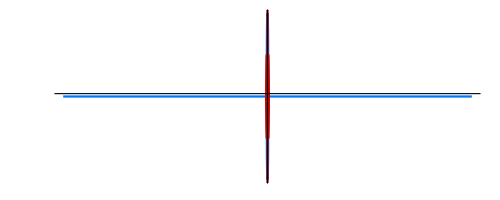

```mathematica
Show[%17,AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.32]],Method->{"ScalingFunctions"->None}]
```

```mathematica
z Abs@z
```

(x+ⅈ y) Abs[x+ⅈ y]

```mathematica
ComplexExpand[(x+ⅈ y) Abs[x+ⅈ y]]
```

x √(x^2+y^2)+ⅈ y √(x^2+y^2)

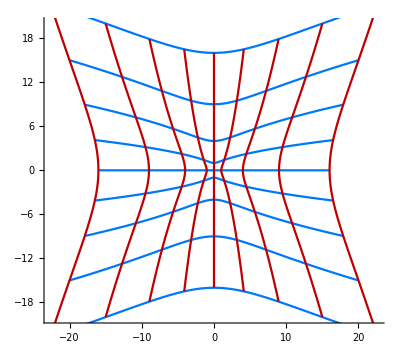

```mathematica
Show[Table[ParametricPlot[{x √(x^2+i^2),i √(x^2+i^2)},{x,-4,4},PlotStyle->RGBColor[0.,0.47,0.98]],{i,-4,4}],Table[ParametricPlot[{i √(i^2+y^2),y √(i^2+y^2) },{y,-4,4},PlotStyle->RGBColor[0.75,0.,0.]],{i,-4,4}],PlotRange->{-20,20}]
```

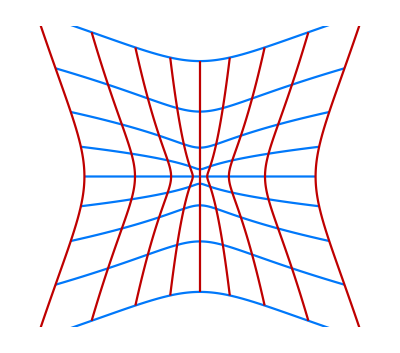

```mathematica
Show[%27,Axes->False]
```

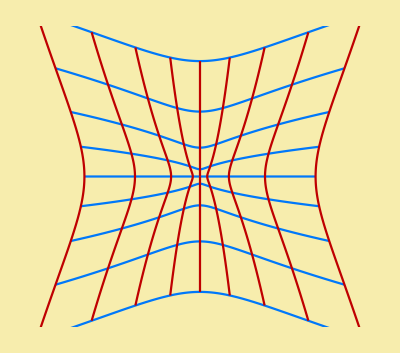

```mathematica
Show[%28,Background->RGBColor[0.97,0.93,0.68]]
```

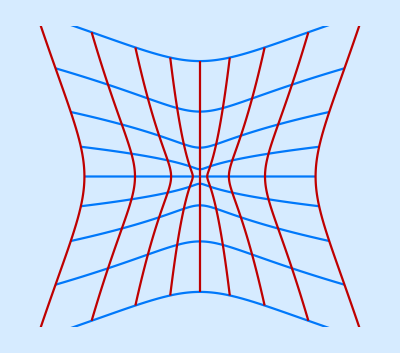

```mathematica
Show[%29,Background->RGBColor[0.84,0.92,1.]]
```